## use blackman from http://mathworld.wolfram.com/BlackmanFunction.html and corresponding instrumentation function for fit.

1.32341×10^-6

6.325×10^-6-7.84325×10^-21 ⅈ

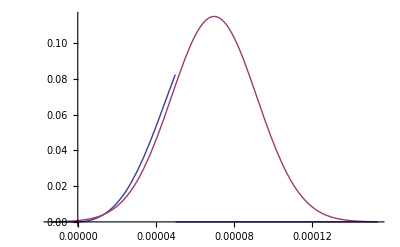

```mathematica
Clear["Global`*"]
us=10^-6;
tRaman=50 us;
ampF4=.115;
square=(HeavisideTheta[t]-HeavisideTheta[t-tRaman]);

blackman=ampF4 square(-1/2 Cos[2π t/tRaman]+2/25 Cos[4π t/tRaman]+21/50);
FWHM=tRaman ;
σ=FWHM/(2 √(2 Log[2]));
t0=tRaman/2;
gauss=ampF4 Exp[-(t-t0)^2/(2 σ^2)];
gauss=ampF4 Exp[-(t-1.26943*1.1*tRaman)^2/((1.1*tRaman)/(√π))^2];
tBlackman=2.79tRaman;
square=(HeavisideTheta[t]-HeavisideTheta[t-tRaman]);
blackman=ampF4 square(-1/2 Cos[2π t/tBlackman]+2/25 Cos[4π t/tBlackman]+21/50);
Integrate[blackman,{t,-Infinity,Infinity}]
Integrate[gauss,{t,-Infinity,Infinity}]
Plot[{blackman,gauss},{t,-.1 tBlackman,1.1tBlackman}]
```

$Aborted

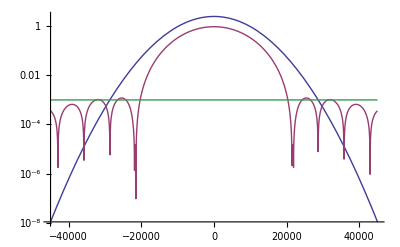

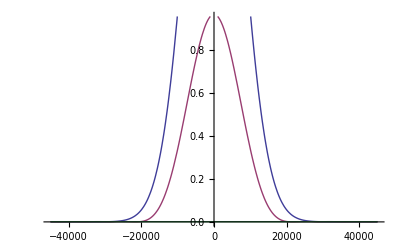

```mathematica
ftbm1=FourierTransform[blackman,t,ω]1/us/.ω->2π f;
ftg=FourierTransform[gauss,t,ω]1/us/.ω->2π f;
ftbm2=1.15((0.84-0.36 (tBlackman/2)^2 f^2)Sinc[π tBlackman f])/((1-(tBlackman/2)^2 f^2)(1-4 (tBlackman/2)^2 f^2));

LogPlot[{Abs[ftg],Abs[ftbm2],Abs[ftbm1],1 10^-3},{f,-(2π)/tBlackman,(2π)/tBlackman}]
Plot[{Abs[ftg],Abs[ftbm2],Abs[ftbm1],1 10^-3},{f,-(2π)/tBlackman,(2π)/tBlackman}]
```